```mathematica
Clear["Global`*"]
ω = {4, -1};
fx = D[{-x^3, -x^2}, x];
fxx = D[fx, x];
fxxx = D[fxx, x];
fxy = D[fx, y];
fxyy = D[fxy, y];
fy = D[{-x^3, -x^2}, y];
fyy = D[fy, y];
gx = D[ {2y^3, 2x^2}, x];
gxx = D[gx, x];
gxxy = D[gxx, x];
gxy = D[gx, y];
gy = D[{2y^3, 2x^2}, y];
gyy = D[gy, y];
gyyy = D[gyy, y];
Solve[16a == fxxx[[1]] + fxyy[[1]] + gxxy[[1]] + gyyy[[1]] + 1/ω[[1]]*(fxy[[1]]*(fxx[[1]] + fyy[[1]]) - gxy[[1]]*(gxx[[1]] + gyy[[1]]) - fxx[[1]]*gxx[[1]] + fyy[[1]]*gyy[[1]]), a]
Solve[16a == fxxx[[2]] + fxyy[[2]] + gxxy[[2]] + gyyy[[2]] + 1/ω[[2]]*(fxy[[2]]*(fxx[[2]] + fyy[[2]]) - gxy[[2]]*(gxx[[2]] + gyy[[2]]) - fxx[[2]]*gxx[[2]] + fyy[[2]]*gyy[[2]]), a]
```

{{a→3/8}}

{{a→-1/2}}

NDSolve::ndinnt: Initial condition x0 is not a number or a rectangular array of numbers.

NDSolve::ndsz: At t == 0.0271175, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 0.0289786, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 0.0310377, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {-0.999959} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

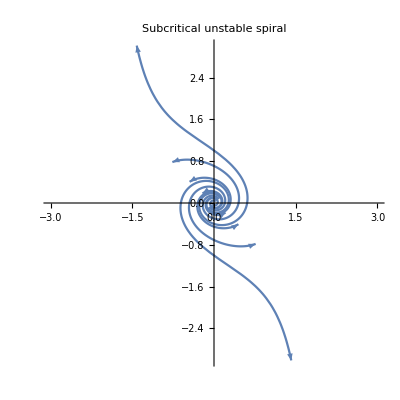

```mathematica
Clear["Global`*"]
minx=-3;  maxx=3; miny=-3; maxy=3;
s[x0_, y0_]=NDSolve[{x'[t]==μ*x[t]-4 y[t]-x[t]^3,y'[t]==4 x[t]+μ*y[t]+2 y[t]^3,x[0]==x0,y[0]==y0}/. μ->1,{x,y},{t,-1,1}];
initialCondition=Join[Table[{0,y},{y,miny,maxy,0.1}],Table[{minx,y},{y,miny,maxy,0.1}],Table[{maxx,y},{y,miny,maxy,0.1}],Table[{x,miny},{x,minx,maxx,0.1}],Table[{x,maxy},{x,minx,maxx,0.1}]];
Show[Table[ParametricPlot[Evaluate[{x[t],y[t]}/. s[initialCondition[[i,1]],initialCondition[[i,2]]]],{t,-1,1},PlotRange->{{minx,maxx},{miny,maxy}}],{i,Length[initialCondition]}]/. Line[x_]:>{Arrowheads[{0.,0.05, 0.05, 0.05, 0.}],Arrow[x]}, PlotLabel-> "Subcritical unstable spiral"]
```

NDSolve::ndinnt: Initial condition x0 is not a number or a rectangular array of numbers.

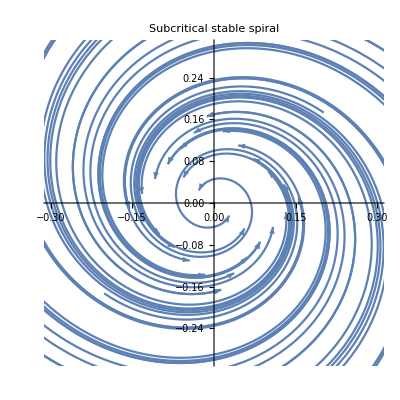

```mathematica
Clear["Global`*"]
minx=-0.3;  maxx=0.3; miny=-0.3; maxy=0.3;
s[x0_, y0_]=NDSolve[{x'[t]==μ*x[t]-4 y[t]-x[t]^3,y'[t]==4 x[t]+μ*y[t]+2 y[t]^3,x[0]==x0,y[0]==y0}/. μ->-1,{x,y},{t,-1,1}];
initialCondition=Join[Table[{0,y},{y,miny,maxy,0.1}],Table[{minx,y},{y,miny,maxy,0.1}],Table[{maxx,y},{y,miny,maxy,0.1}],Table[{x,miny},{x,minx,maxx,0.1}],Table[{x,maxy},{x,minx,maxx,0.1}]];
Show[Table[ParametricPlot[Evaluate[{x[t],y[t]}/. s[initialCondition[[i,1]],initialCondition[[i,2]]]],{t,-1,1},PlotRange->{{minx,maxx},{miny,maxy}}],{i,Length[initialCondition]}]/. Line[x_]:>{Arrowheads[{0.,0.05, 0.05, 0.05, 0.}],Arrow[x]}, PlotLabel-> "Subcritical stable spiral"]
```

NDSolve::ndinnt: Initial condition x0 is not a number or a rectangular array of numbers.

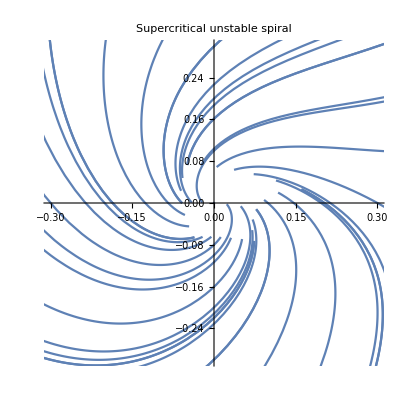

```mathematica
Clear["Global`*"]
minx=-0.3;  maxx=0.3; miny=-0.3; maxy=0.3;
s[x0_, y0_]=NDSolve[{x'[t]==μ*x[t]+ y[t]-x[t]^2,y'[t]==-x[t]+μ*y[t]+2 x[t]^2,x[0]==x0,y[0]==y0}/. μ->1,{x,y},{t,-1.5,1.5}];
initialCondition=Join[Table[{0,y},{y,miny,maxy,0.1}],Table[{minx,y},{y,miny,maxy,0.1}],Table[{maxx,y},{y,miny,maxy,0.1}],Table[{x,miny},{x,minx,maxx,0.1}],Table[{x,maxy},{x,minx,maxx,0.1}]];
Show[Table[ParametricPlot[Evaluate[{x[t],y[t]}/. s[initialCondition[[i,1]],initialCondition[[i,2]]]],{t,-1.5,1.5},PlotRange->{{minx,maxx},{miny,maxy}}],{i,Length[initialCondition]}]/. Line[x_]:>{Arrowheads[{0.,0.05, 0.05, 0.05, 0.}],Arrow[x]}, PlotLabel-> "Supercritical unstable spiral"]
```

NDSolve::ndinnt: Initial condition x0 is not a number or a rectangular array of numbers.

NDSolve::ndsz: At t == -1.10177, step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction::dmval: Input value {-1.49994} lies outside the range of data in the interpolating function. Extrapolation will be used.

NDSolve::ndsz: At t == -1.17309, step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction::dmval: Input value {-1.49994} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NDSolve::ndsz: At t == -1.26898, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

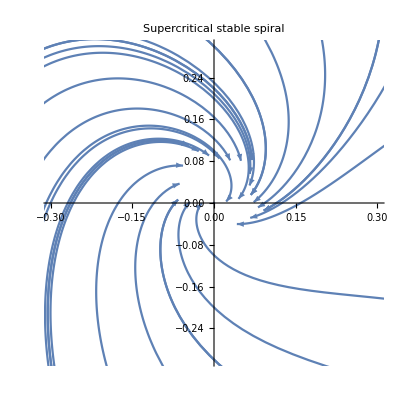

```mathematica
Clear["Global`*"]
minx=-0.3;  maxx=0.3; miny=-0.3; maxy=0.3;
s[x0_, y0_]=NDSolve[{x'[t]==μ*x[t]+ y[t]-x[t]^2,y'[t]==-x[t]+μ*y[t]+2 x[t]^2,x[0]==x0,y[0]==y0}/. μ->-1,{x,y},{t,-1.5,1.5}];
initialCondition=Join[Table[{0,y},{y,miny,maxy,0.1}],Table[{minx,y},{y,miny,maxy,0.1}],Table[{maxx,y},{y,miny,maxy,0.1}],Table[{x,miny},{x,minx,maxx,0.1}],Table[{x,maxy},{x,minx,maxx,0.1}]];
Show[Table[ParametricPlot[Evaluate[{x[t],y[t]}/. s[initialCondition[[i,1]],initialCondition[[i,2]]]],{t,-1.5,1.5},PlotRange->{{minx,maxx},{miny,maxy}}],{i,Length[initialCondition]}]/. Line[x_]:>{Arrowheads[{0.,0.05, 0.05, 0.05, 0.}],Arrow[x]}, PlotLabel-> "Supercritical stable spiral"]
```